-Graphics-

-Graphics-

-Graphics-

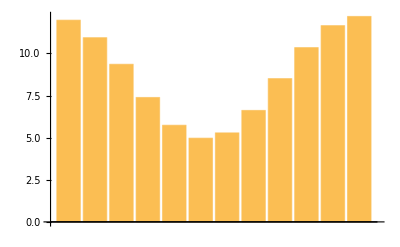

```mathematica
SOLAR=1367;
DiasJulianos=List[17,47,75,105,135,162,198,228,258,288,318,344];
Hs=List[7.689,6.804,5.714,4.238,3.323,2.821,2.989,3.805,5.167,6.224,7.244,7.541];
latitud=-31.4°; (* ϕ *)
inclinacion=latitud; (* β *)
acimut=Pi; (* γ *)
anguloSolar=(h-12)Pi/12;  (* ω *)
declinacion=(23.45*Pi/180)*Sin[2*Pi*(284+n)/365]; (* δ *)
cenit=ArcCos[ Cos[latitud]Cos[declinacion]Cos[anguloSolar]+Sin[latitud]Sin[declinacion]];
acimutSolar=If[anguloSolar<0,-1,1]Abs[ArcCos[(Cos[cenit]Sin[latitud]-Sin[declinacion])/(Sin[cenit]Cos[latitud])]];
incidencia=ArcCos[Cos[cenit]Cos[inclinacion]+Sin[cenit]Sin[inclinacion]Cos[acimutSolar-acimut]];
excentricidad = 1+0.033Cos[2Pi*n/365];
anguloSalida=ArcCos[-Tan[declinacion]Tan[latitud]];
HoJ=(24*3600/Pi)*SOLAR*excentricidad(Cos[latitud]*Cos[declinacion]*Sin[anguloSalida]+anguloSalida*Sin[latitud]Sin[declinacion]);
Ho=HoJ/3600000;
angulo1=anguloSolar-Pi/24;
angulo2=anguloSolar+Pi/24;
IoJ=(12*3600/Pi)*SOLAR*excentricidad(Cos[latitud]Cos[declinacion](Sin[angulo2]-Sin[angulo1])+(angulo2-angulo1)Sin[latitud]Sin[declinacion]);
Io=IoJ/3600000;
a=0.409+0.5016Sin[anguloSalida-Pi/3];
b=0.6609-0.4767Sin[anguloSalida-Pi/3];
rt=Pi/24*(a+b*Cos[anguloSolar])*(Cos[anguloSolar]-Cos[anguloSalida])/(Sin[anguloSalida]-anguloSalida*Cos[anguloSalida]);
IH=H*rt;
kT=IH/Io;
Id =IH*Which[
kT<=0.22,1-0.09kT,
kT<=0.80,0.9511-0.1604kT+4.388kT^2-16.638kT^3+12.336kT^4,
True,0.165
];
(*Rb=Cos[incidencia]/Cos[cenit];*)
Block[{n=DiasJulianos[[1]]},
Plot[{anguloSolar,cenit,acimutSolar,incidencia},{h, 0, 24},
PlotLabel->"Ángulos solares durante 24 horas",
PlotLabels->{"Ángulo horario", "Ángulo cenital", "Ángulo acimutal", "Ángulo de incidencia con el panel"}
]
]
Block[{h=12},
Plot[{excentricidad, declinacion},{n, 1, 365},
PlotLabel->"Valores dependientes de la epoca del año",
PlotLabels->{"Excentricidad", "Declinación"}
]
]
Block[{n=DiasJulianos[[6]], H=Hs[[1]]},
Plot[{Io, IH, Id},{h, 0, 24},
PlotLabel->"Irradiación horaria en superficie horizontal",
PlotLabels->{"A tope de atmósfera", "En tierra", "Difusa"},
PlotHighlighting->"XSlice"
]
]
BarChart[Block[{n=#[[1]], H=#[[2]]}, Ho] &/@Transpose[{DiasJulianos, Hs}]]
```